# C++ Class Layout Parser - Comprehensive Inheritance Testing

This notebook demonstrates the C++ Class Layout Parser tool by testing various inheritance patterns and visualizing memory layouts. The parser uses clang's JSON AST via CppClassLayoutParser.wl.

## Setup and Initialization

```mathematica
(* Clear definitions and load parser *)
Remove["CppClassLayoutParser`*"];
SetDirectory[NotebookDirectory[]];
<< "../CppClassLayoutParser.wl"
```

## Test Overview Table

```mathematica
{{"Test #", "Pattern", "Description", "File", "Target Class"}, {"Test 1", "Simple Single Class", "Basic VTable creation", "simple_single_class.hpp", "SimpleClass"}, {"Test 2", "Single Inheritance", "Basic inheritance hierarchy", "single_inheritance.hpp", "Derived"}, {"Test 3", "Multiple Inheritance", "Multiple base classes", "multiple_inheritance.hpp", "MultipleDerived"}, {"Test 4", "Virtual Inheritance", "Shared virtual bases", "virtual_inheritance.hpp", "VirtualMultiple"}, {"Test 5", "Diamond Inheritance", "Classic diamond problem", "diamond_inheritance.hpp", "DiamondBottom"}, {"Test 6", "Complex Inheritance", "Mixed virtual/non-virtual", "complex_inheritance.hpp", "Z"}, {"Test 7", "Deep Inheritance", "5-level hierarchy", "deep_inheritance.hpp", "Level5"}, {"Test 8", "Interface Inheritance", "Abstract classes", "interface_inheritance.hpp", "MultiInterface"}, {"Test 9", "Template Inheritance", "Template instantiation", "template_inheritance.hpp", "DoubleDerived"}, {"Test 10", "Extreme Complexity", "Multiple virtual bases & deep hier.", "extreme_complexity.hpp", "UltimateComplex"}}
```

## Test 1: Simple Single Class

=== Contents of “simple_single_class.hpp” ===

// Simple single class with virtual functions
class SimpleClass {
public:
    virtual void method1() {}
    virtual void method2() {}
    virtual ~SimpleClass() {}
    
private:
    int data1;
    double data2;
};

=== Layout for “SimpleClass” ===

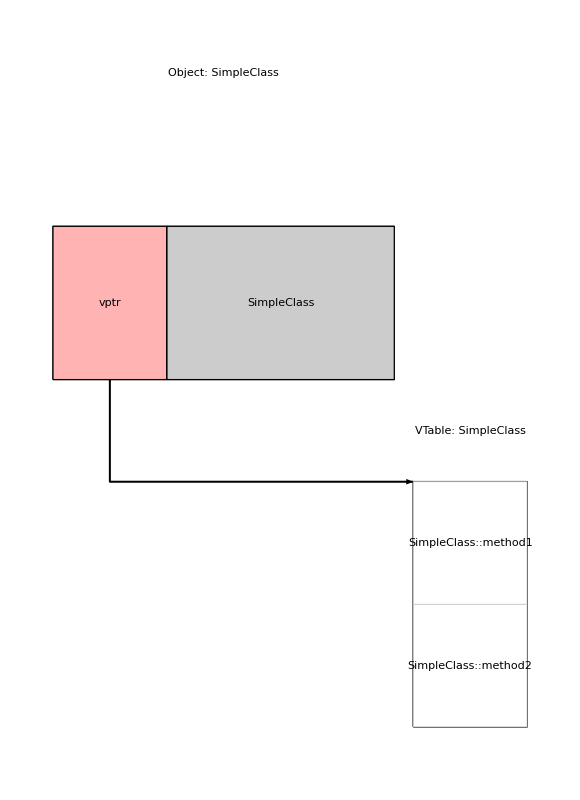

```mathematica
(* Basic VTable creation *)
(* 1. Read and print the C++ source file *)
code = Import["simple_single_class.hpp", "Text"];
Print["=== Contents of “simple_single_class.hpp” ==="];
Print[code];

(* 2. Parse & visualize *)
result = ParseAndDrawClassLayout["simple_single_class.hpp", "SimpleClass"];
Print["=== Layout for “SimpleClass” ==="];
Print[result];
```

## Test 2: Single Inheritance

=== Contents of “single_inheritance.hpp” ===

// Single inheritance example
class Base {
public:
    virtual void baseMethod() {}
    virtual ~Base() {}
    
private:
    int baseData;
};

class Derived : public Base {
public:
    virtual void derivedMethod() {}
    virtual void baseMethod() override {}
    virtual ~Derived() {}
    
private:
    double derivedData;
};

=== Layout for “Derived” ===

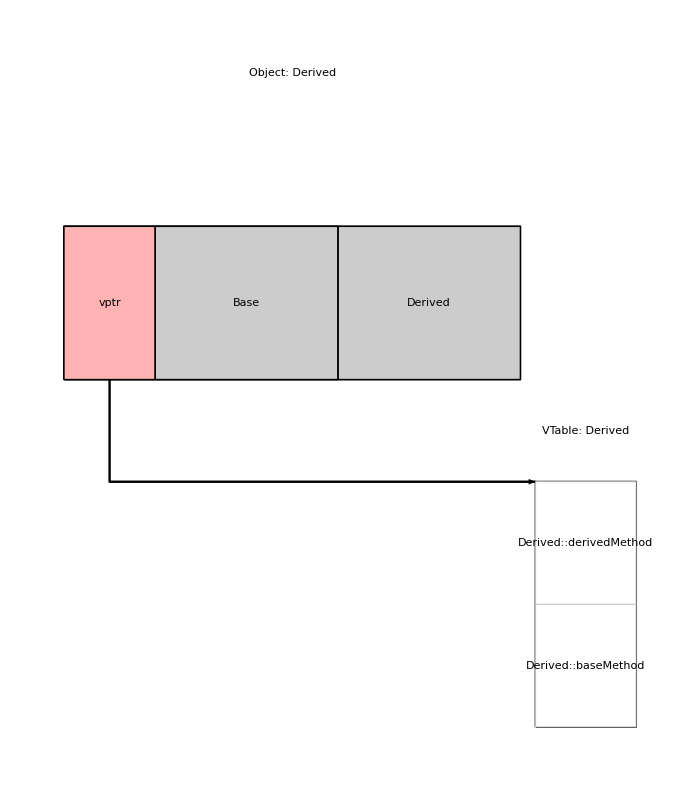

```mathematica
(* Basic inheritance hierarchy *)
(* 1. Read and print the C++ source file *)
code = Import["single_inheritance.hpp", "Text"];
Print["=== Contents of “single_inheritance.hpp” ==="];
Print[code];

(* 2. Parse & visualize *)
result = ParseAndDrawClassLayout["single_inheritance.hpp", "Derived"];
Print["=== Layout for “Derived” ==="];
Print[result];
```

## Test 3: Multiple Inheritance

=== Contents of “multiple_inheritance.hpp” ===

// Multiple inheritance example
class Base1 {
public:
    virtual void base1Method() {}
    virtual ~Base1() {}
    
private:
    int base1Data;
};

class Base2 {
public:
    virtual void base2Method() {}
    virtual ~Base2() {}
    
private:
    double base2Data;
};

class MultipleDerived : public Base1, public Base2 {
public:
    virtual void derivedMethod() {}
    virtual void base1Method() override {}
    virtual void base2Method() override {}
    virtual ~MultipleDerived() {}
    
private:
    char derivedData;
};

=== Layout for “MultipleDerived” ===

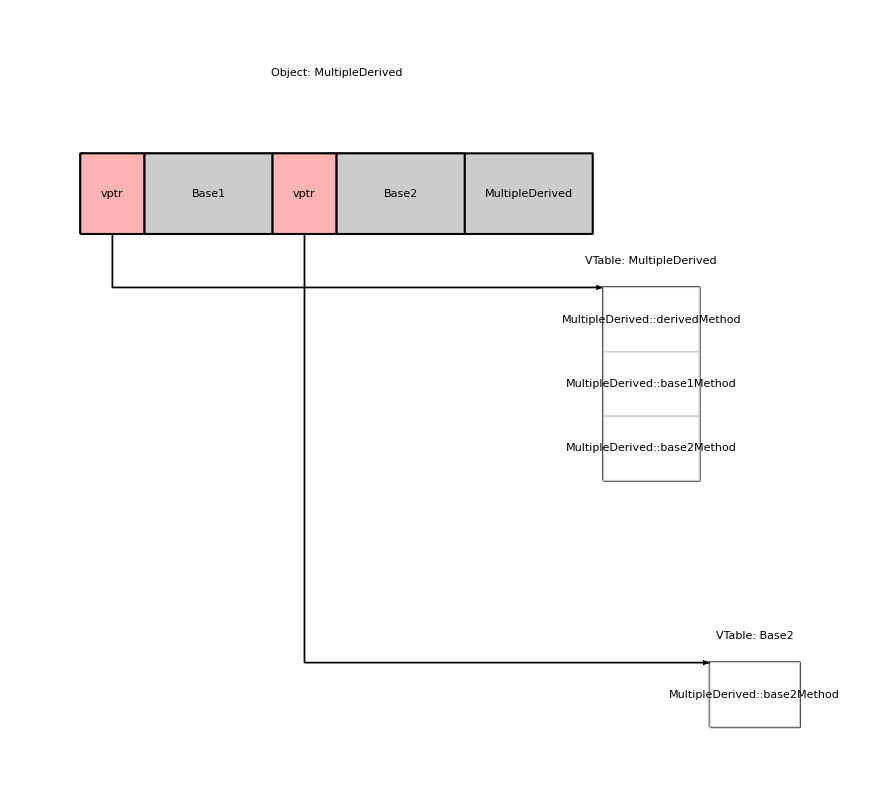

```mathematica
(* Multiple base classes *)
(* 1. Read and print the C++ source file *)
code = Import["multiple_inheritance.hpp", "Text"];
Print["=== Contents of “multiple_inheritance.hpp” ==="];
Print[code];

(* 2. Parse & visualize *)
result = ParseAndDrawClassLayout["multiple_inheritance.hpp", "MultipleDerived"];
Print["=== Layout for “MultipleDerived” ==="];
Print[result];
```

## Test 4: Virtual Inheritance

=== Contents of “virtual_inheritance.hpp” ===

// Virtual inheritance example
class VirtualBase {
public:
    virtual void virtualBaseMethod() {}
    virtual ~VirtualBase() {}
    
private:
    int virtualBaseData;
};

class VirtualDerived1 : virtual public VirtualBase {
public:
    virtual void derived1Method() {}
    virtual ~VirtualDerived1() {}
    
private:
    double derived1Data;
};

class VirtualDerived2 : virtual public VirtualBase {
public:
    virtual void derived2Method() {}
    virtual ~VirtualDerived2() {}
    
private:
    char derived2Data;
};

class VirtualMultiple : public VirtualDerived1, public VirtualDerived2 {
public:
    virtual void multipleMethod() {}
    virtual ~VirtualMultiple() {}
    
private:
    float multipleData;
};

=== Layout for “VirtualMultiple” ===

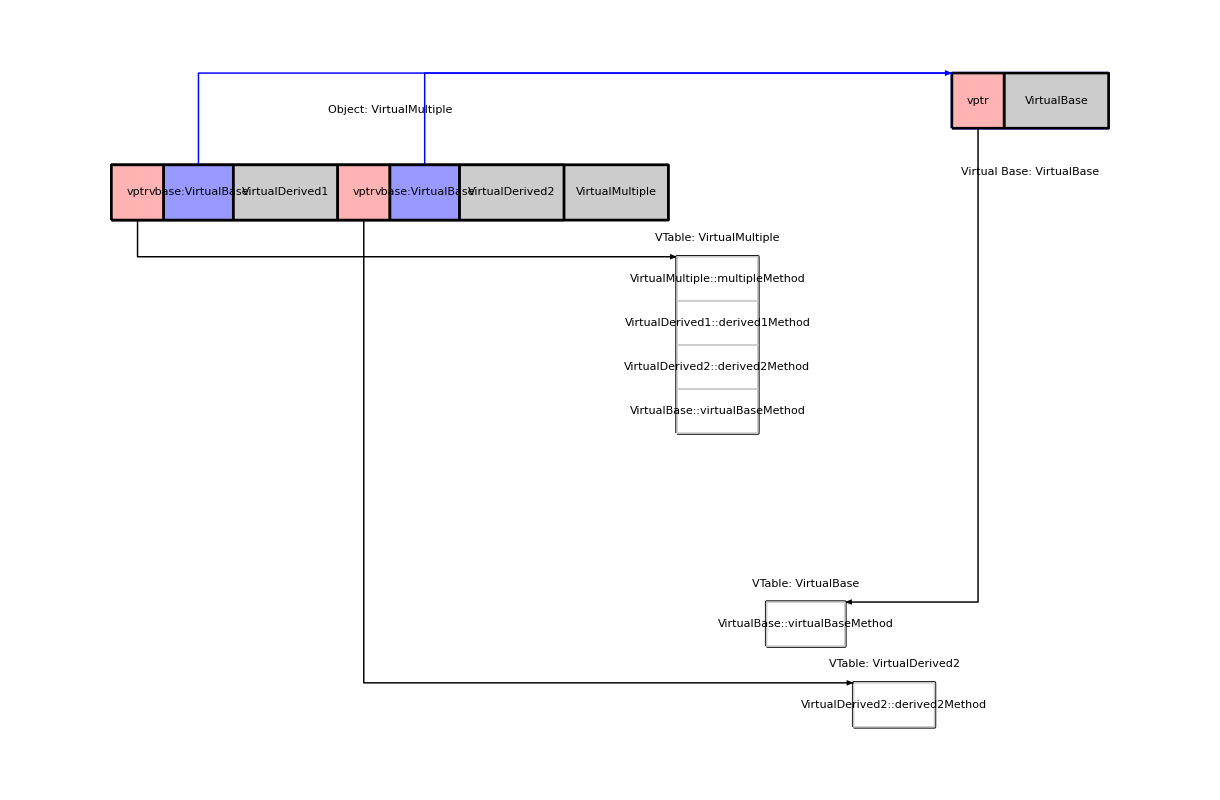

```mathematica
(* Shared virtual bases *)
(* 1. Read and print the C++ source file *)
code = Import["virtual_inheritance.hpp", "Text"];
Print["=== Contents of “virtual_inheritance.hpp” ==="];
Print[code];

(* 2. Parse & visualize *)
result = ParseAndDrawClassLayout["virtual_inheritance.hpp", "VirtualMultiple"];
Print["=== Layout for “VirtualMultiple” ==="];
Print[result];
```

## Test 5: Diamond Inheritance

=== Contents of “diamond_inheritance.hpp” ===

// Classic diamond inheritance problem
class DiamondBase {
public:
    virtual void diamondMethod() {}
    virtual ~DiamondBase() {}
    
private:
    int diamondData;
};

class DiamondLeft : virtual public DiamondBase {
public:
    virtual void leftMethod() {}
    virtual void diamondMethod() override {}
    virtual ~DiamondLeft() {}
    
private:
    double leftData;
};

class DiamondRight : virtual public DiamondBase {
public:
    virtual void rightMethod() {}
    virtual void diamondMethod() override {}
    virtual ~DiamondRight() {}
    
private:
    char rightData;
};

class DiamondBottom : public DiamondLeft, public DiamondRight {
public:
    virtual void bottomMethod() {}
    virtual void diamondMethod() override {}
    virtual ~DiamondBottom() {}
    
private:
    float bottomData;
};

=== Layout for “DiamondBottom” ===

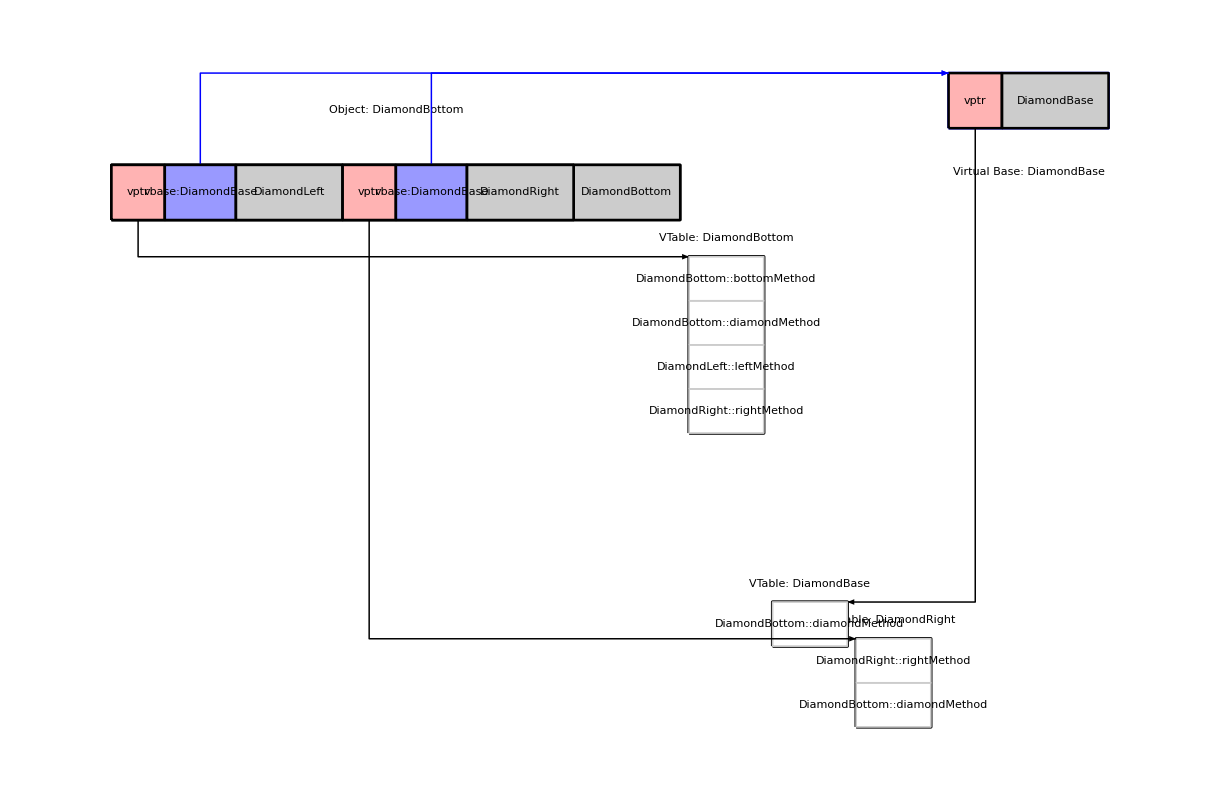

```mathematica
(* Classic diamond problem *)
(* 1. Read and print the C++ source file *)
code = Import["diamond_inheritance.hpp", "Text"];
Print["=== Contents of “diamond_inheritance.hpp” ==="];
Print[code];

(* 2. Parse & visualize *)
result = ParseAndDrawClassLayout["diamond_inheritance.hpp", "DiamondBottom"];
Print["=== Layout for “DiamondBottom” ==="];
Print[result];
```

## Test 6: Complex Inheritance

=== Contents of “complex_inheritance.hpp” ===

// Complex inheritance with mixed virtual and non-virtual inheritance
class X {
public:
    virtual void xMethod() {}
    virtual ~X() {}
    
private:
    int xData;
};

class Y1 : public X {
public:
    virtual void y1Method() {}
    virtual void xMethod() override {}
    virtual ~Y1() {}
    
private:
    double y1Data;
};

class Y2 : virtual public X {
public:
    virtual void y2Method() {}
    virtual void xMethod() override {}
    virtual ~Y2() {}
    
private:
    char y2Data;
};

class Z : public Y1, public Y2 {
public:
    virtual void zMethod() {}
    virtual void xMethod() override {}
    virtual ~Z() {}
    
private:
    float zData;
};

=== Layout for “Z” ===

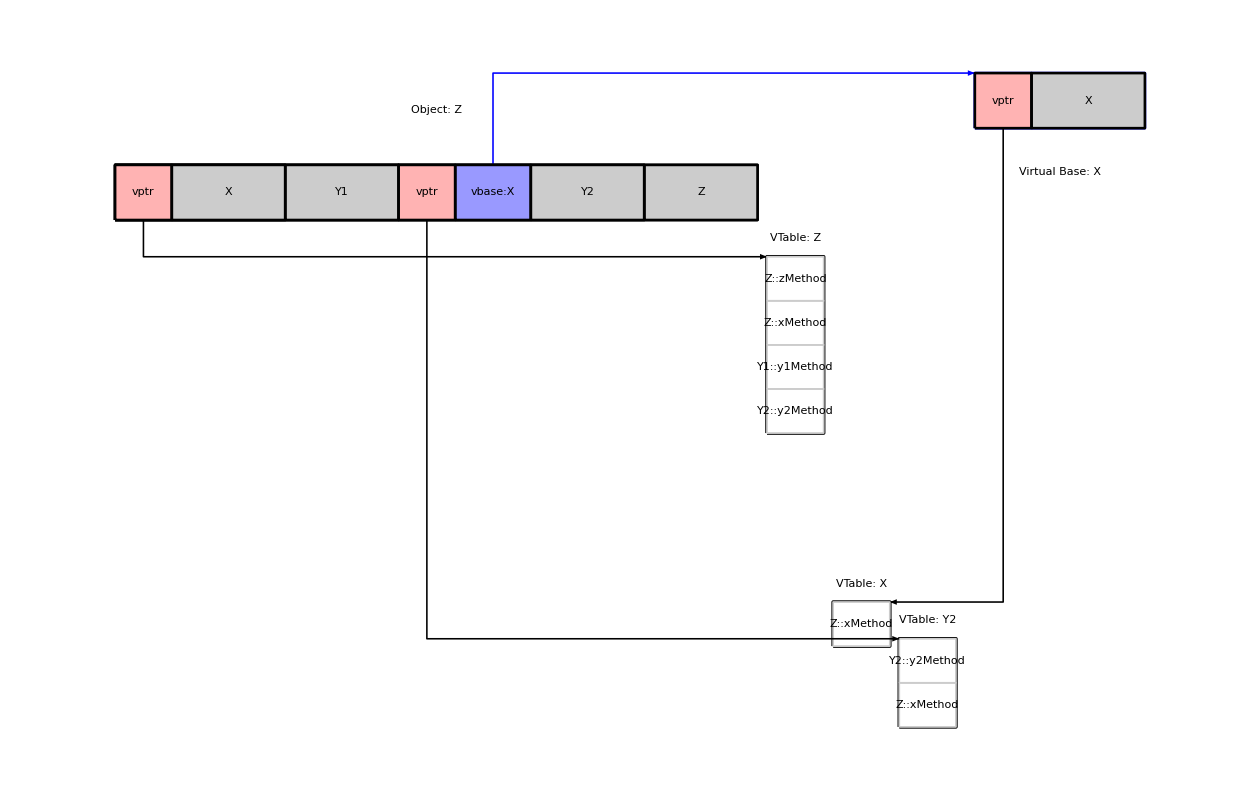

```mathematica
(* Mixed virtual/non-virtual *)
(* 1. Read and print the C++ source file *)
code = Import["complex_inheritance.hpp", "Text"];
Print["=== Contents of “complex_inheritance.hpp” ==="];
Print[code];

(* 2. Parse & visualize *)
result = ParseAndDrawClassLayout["complex_inheritance.hpp", "Z"];
Print["=== Layout for “Z” ==="];
Print[result];
```

## Test 7: Deep Inheritance

=== Contents of “deep_inheritance.hpp” ===

// Deep inheritance hierarchy
class Level1 {
public:
    virtual void level1Method() {}
    virtual ~Level1() {}
    
private:
    int level1Data;
};

class Level2 : public Level1 {
public:
    virtual void level2Method() {}
    virtual void level1Method() override {}
    virtual ~Level2() {}
    
private:
    double level2Data;
};

class Level3 : public Level2 {
public:
    virtual void level3Method() {}
    virtual void level2Method() override {}
    virtual ~Level3() {}
    
private:
    char level3Data;
};

class Level4 : public Level3 {
public:
    virtual void level4Method() {}
    virtual void level3Method() override {}
    virtual ~Level4() {}
    
private:
    float level4Data;
};

class Level5 : public Level4 {
public:
    virtual void level5Method() {}
    virtual void level4Method() override {}
    virtual ~Level5() {}
    
private:
    long level5Data;
};

=== Layout for “Level5” ===

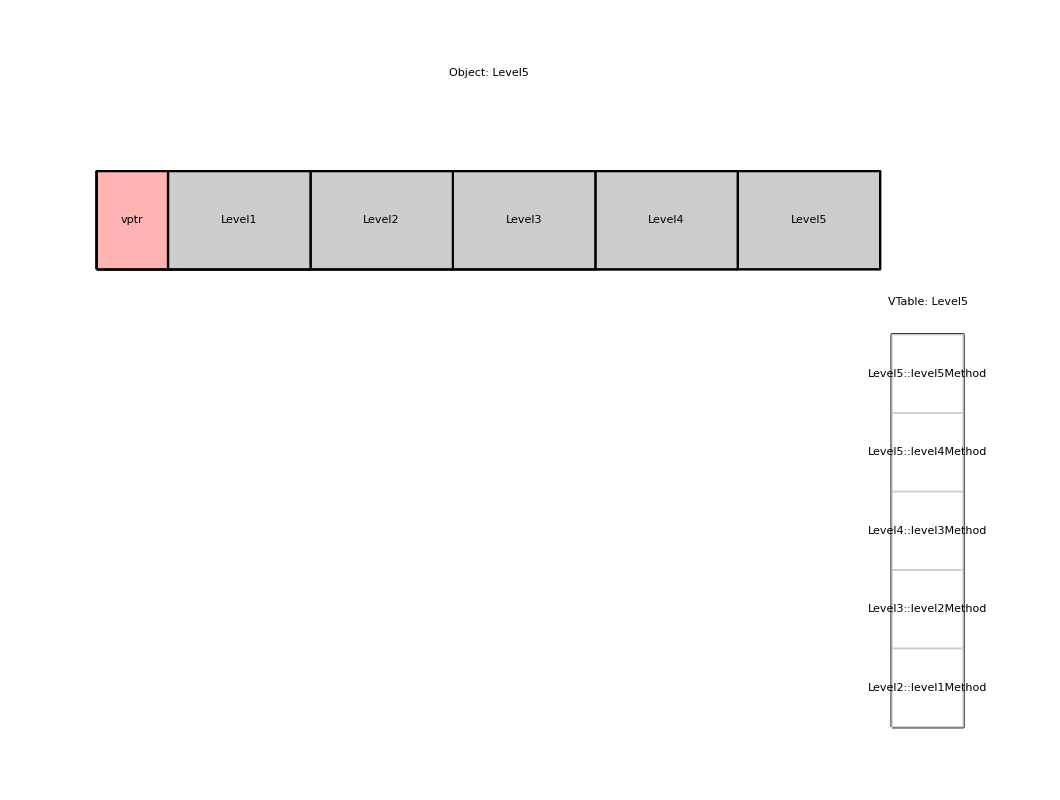

```mathematica
(* 5-level hierarchy *)
(* 1. Read and print the C++ source file *)
code = Import["deep_inheritance.hpp", "Text"];
Print["=== Contents of “deep_inheritance.hpp” ==="];
Print[code];

(* 2. Parse & visualize *)
result = ParseAndDrawClassLayout["deep_inheritance.hpp", "Level5"];
Print["=== Layout for “Level5” ==="];
Print[result];
```

## Test 8: Interface Inheritance

=== Contents of “interface_inheritance.hpp” ===

// Interface-based inheritance example
class Interface1 {
public:
    virtual void interface1Method() = 0;
    virtual ~Interface1() = default;
};

class Interface2 {
public:
    virtual void interface2Method() = 0;
    virtual ~Interface2() = default;
};

class ConcreteBase {
public:
    virtual void concreteMethod() {}
    virtual ~ConcreteBase() {}
    
private:
    int concreteData;
};

class InterfaceImpl1 : public Interface1, public ConcreteBase {
public:
    virtual void interface1Method() override {}
    virtual void concreteMethod() override {}
    virtual ~InterfaceImpl1() {}
    
private:
    double impl1Data;
};

class InterfaceImpl2 : public Interface2, public ConcreteBase {
public:
    virtual void interface2Method() override {}
    virtual void concreteMethod() override {}
    virtual ~InterfaceImpl2() {}
    
private:
    char impl2Data;
};

class MultiInterface : public Interface1, public Interface2, public ConcreteBase {
public:
    virtual void interface1Method() override {}
    virtual void interface2Method() override {}
    virtual void concreteMethod() override {}
    virtual ~MultiInterface() {}
    
private:
    float multiData;
};

=== Layout for “MultiInterface” ===

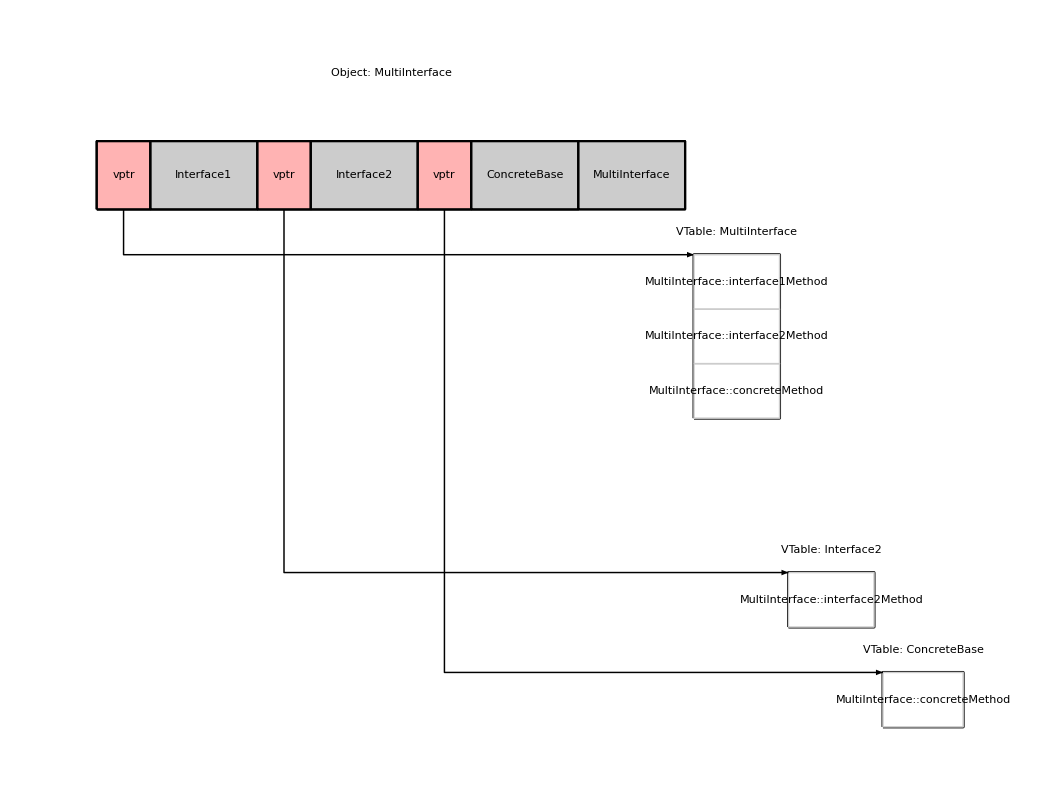

```mathematica
(* Abstract classes *)
(* 1. Read and print the C++ source file *)
code = Import["interface_inheritance.hpp", "Text"];
Print["=== Contents of “interface_inheritance.hpp” ==="];
Print[code];

(* 2. Parse & visualize *)
result = ParseAndDrawClassLayout["interface_inheritance.hpp", "MultiInterface"];
Print["=== Layout for “MultiInterface” ==="];
Print[result];
```

## Test 9: Extreme Complexity

=== Contents of “extreme_complexity.hpp” ===

// Extreme complexity example with multiple virtual bases and deep hierarchies
class VirtualRoot1 {
public:
    virtual void vr1Method() {}
    virtual ~VirtualRoot1() {}
    
private:
    int vr1Data;
};

class VirtualRoot2 {
public:
    virtual void vr2Method() {}
    virtual ~VirtualRoot2() {}
    
private:
    double vr2Data;
};

class VirtualRoot3 {
public:
    virtual void vr3Method() {}
    virtual ~VirtualRoot3() {}
    
private:
    char vr3Data;
};

class Middle1 : virtual public VirtualRoot1, virtual public VirtualRoot2 {
public:
    virtual void middle1Method() {}
    virtual void vr1Method() override {}
    virtual void vr2Method() override {}
    virtual ~Middle1() {}
    
private:
    float middle1Data;
};

class Middle2 : virtual public VirtualRoot2, virtual public VirtualRoot3 {
public:
    virtual void middle2Method() {}
    virtual void vr2Method() override {}
    virtual void vr3Method() override {}
    virtual ~Middle2() {}
    
private:
    long middle2Data;
};

class Middle3 : virtual public VirtualRoot1, virtual public VirtualRoot3 {
public:
    virtual void middle3Method() {}
    virtual void vr1Method() override {}
    virtual void vr3Method() override {}
    virtual ~Middle3() {}
    
private:
    short middle3Data;
};

class ComplexDerived1 : public Middle1, public Middle2 {
public:
    virtual void complex1Method() {}
    virtual void vr1Method() override {}
    virtual void vr2Method() override {}
    virtual void vr3Method() override {}
    virtual ~ComplexDerived1() {}
    
private:
    int complex1Data;
};

class ComplexDerived2 : public Middle2, public Middle3 {
public:
    virtual void complex2Method() {}
    virtual void vr1Method() override {}
    virtual void vr2Method() override {}
    virtual void vr3Method() override {}
    virtual ~ComplexDerived2() {}
    
private:
    double complex2Data;
};

class UltimateComplex : public ComplexDerived1, public ComplexDerived2 {
public:
    virtual void ultimateMethod() {}
    virtual void vr1Method() override {}
    virtual void vr2Method() override {}
    virtual void vr3Method() override {}
    virtual ~UltimateComplex() {}
    
private:
    char ultimateData;
};

=== Layout for “UltimateComplex” ===

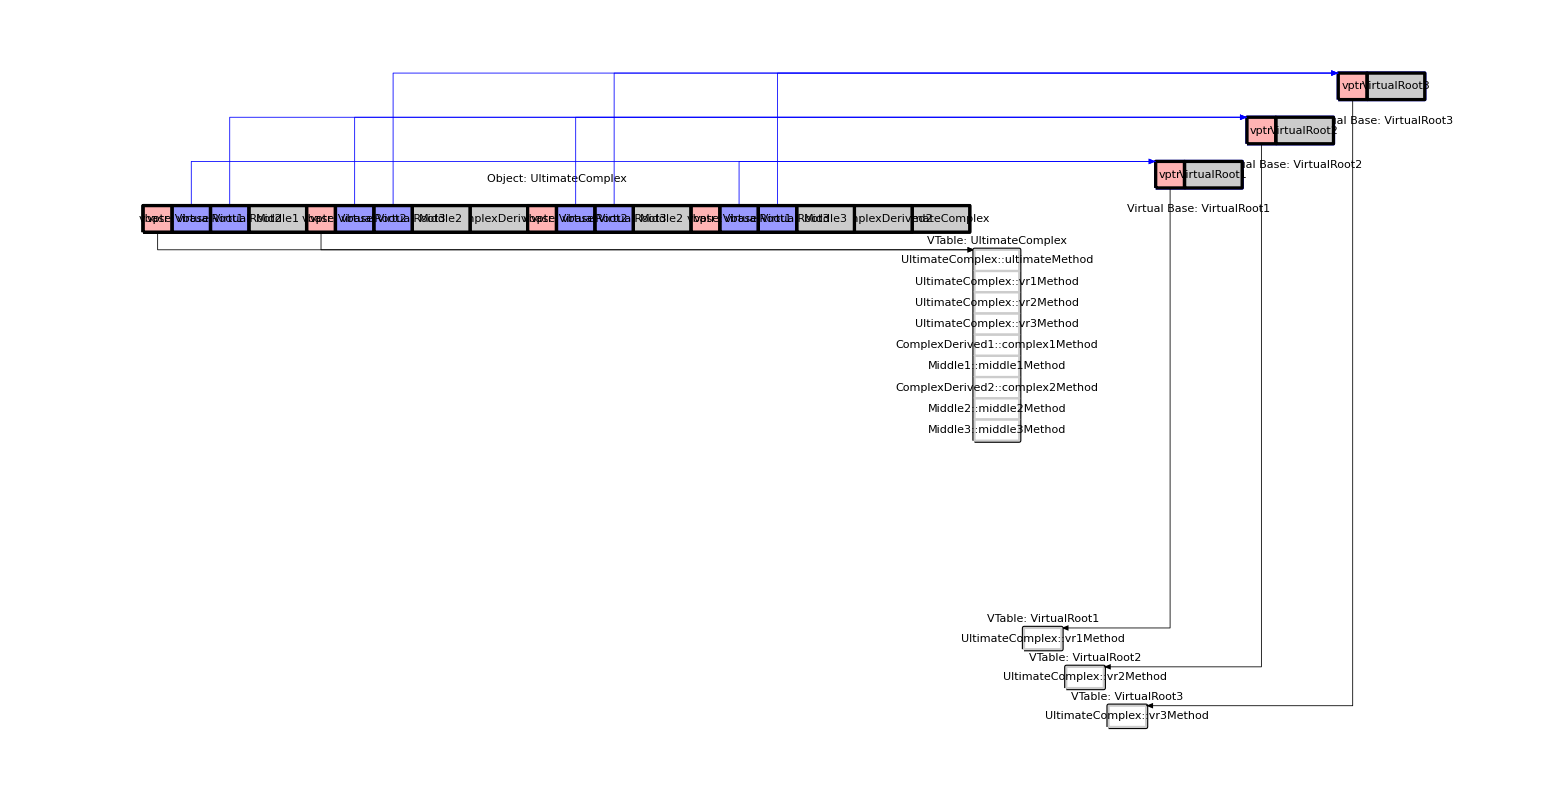

```mathematica
(* Multiple virtual bases & deep hier. *)
(* 1. Read and print the C++ source file *)
code = Import["extreme_complexity.hpp", "Text"];
Print["=== Contents of “extreme_complexity.hpp” ==="];
Print[code];

(* 2. Parse & visualize *)
result = ParseAndDrawClassLayout["extreme_complexity.hpp", "UltimateComplex"];
Print["=== Layout for “UltimateComplex” ==="];
Print[result];
```